```mathematica
Clear["Global`*"]
```

```mathematica
Solve[0==1*(-w+U*r+U*a*(1-c)*(-w+U*(V-1*F*V/2))),V]
```

{{V→-(2 (r U-w-a U w+a c U w))/(a (-1+c) (-2+F) U^2)}}

```mathematica
f[VUJ2_]:={{V->-(2 (r U-w-a U w+a c U w))/(a (-1+c) (-2+F) U^2)}}
```

```mathematica
Solve[0==1*(-w+U*r*+U*a*(1-c)*(-w+U*(V-0*F*V/2))),V]
```

{{V→(-w-a r U^2 w+a c r U^2 w)/(a (-1+c) r U^3)}}

```mathematica
f[VUI1_]:={{V->(-w-a r U^2 w+a c r U^2 w)/(a (-1+c) r U^3)}}
```

```mathematica
Solve[0==1*(0*(-w)+(1*U*a+0*F*a-1*U*a*0*F*a)*(-w+F*V)-(1*U*a*(1-c)*U*F*V/2)),V]
```

{{V→(2 w)/(F (2-U+c U))}}

```mathematica
f[VFJ2_]:={{V->(2 w)/(F (2-U+c U))}}
```

```mathematica
Solve[0==1*(1*(-w)+(1*U*a+1*F*a-1*U*a*1*F*a)*(-w+F*V)-(1*U*a*(1-c)*U*F*V/2)),V]
```

```mathematica
f[VFJ1_]:={{V->(2 (-w-a F w-a U w+a^2 F U w))/(a F (-2 F-2 U+2 a F U+U^2-c U^2))}}
```

```mathematica
Solve[0==1*(1*(-w)+(0*U*a+1*F*a-0*U*a*1*F*a)*(-w+F*V)-(0*U*a*(1-c)*U*F*V/2)),V]
```

{{V→(w+a F w)/(a F^2)}}

```mathematica
f[VFI1_]:={{V->(w+a F w)/(a F^2)}}
```

```mathematica
Solve[0==1*(-w+U*r+U*a*(1-c)*(-w+U*(V-1*F*V/2)))+1*(0*(-w)+(1*U*a+0*F*a-1*U*a*0*F*a)*(-w+F*V)-(1*U*a*(1-c)*U*F*V/2)),V]
```

{{V→(-r U+w+2 a U w-a c U w)/(a U (F+U-c U-F U+c F U))}}

```mathematica
f[SWFVSolve_]:={{V->(-r U+w+2 a U w-a c U w)/(a U (F+U-c U-F U+c F U))}}
```

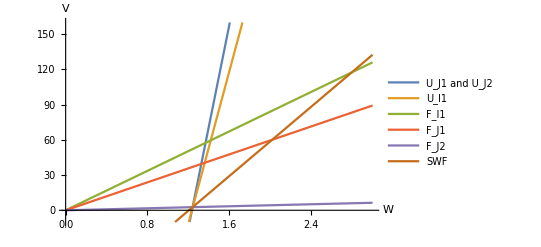

```mathematica
a=0.1; r=5; F=0.5; U=0.25; c=0.5;
fig3swf=Plot[{-(2 (r  U-w-a U w+a c U w))/(a (-1+c) (-2+F) U^2),(r  U-w-a U w+a c U w)/(a (-1+c) U^2),(w+a F w)/(a F^2),(2 (-w-a F w-a U w+a^2 F U w))/(a F (-2 F-2 U+2 a F U+U^2-c U^2)), (2 w)/(F (2-U+c U)),(-r U+w+2 a U w-a c U w)/(a U (F+U-c U-F U+c F U))},{w,0, 3},PlotRange->{-10, 160},PlotLegends->{"U_J1 and U_J2","U_I1", "F_I1","F_J1","F_J2","SWF"},AxesLabel->{ W, V},LabelStyle->FontFamily->"Cambria Math"]
```